# Scattering Kernels in 3D

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Linearly-Anisotropic Scattering (Eddington)

```mathematica
pLinaniso[u_,b_]:=1/(4 Pi)(1+b u)
```

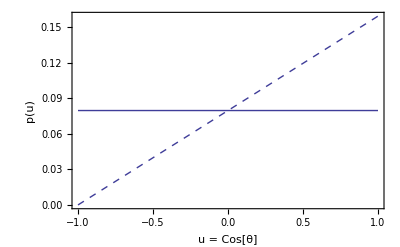

```mathematica
Clear[u];
Show[
Plot[pIsotropic[u],{u,-1,1},PlotStyle->Thick],
Plot[pLinaniso[u,1],{u,-1,1},PlotStyle->Dashed]
,Frame->True,
FrameLabel->{{p[u],},{"u = Cos[θ]","Linearly-Anisotropic Scattering"}}]
```

### Normalization condition

```mathematica
Integrate[2 Pi pLinaniso[u,b],{u,-1,1},Assumptions->b>-1&&b<1]
```

1

### Mean cosine (g)

```mathematica
Integrate[2 Pi pLinaniso[u,b]u,{u,-1,1},Assumptions->b>-1&&b<1]
```

b/3

### Legendre expansion coefficients

```mathematica
Integrate[2Pi(2k+1)pLinaniso[Cos[y],b]LegendreP[k,Cos[y]]Sin[y]/.k->0,{y,0,Pi}]
```

1

```mathematica
Integrate[2Pi(2k+1)pLinaniso[Cos[y],b]LegendreP[k,Cos[y]]Sin[y]/.k->1,{y,0,Pi}]
```

b

### sampling

```mathematica
cdf=Integrate[2 Pi pLinaniso[u,b],{u,-1,x}]
```

1/2-b/4+x/2+(b x^2)/4

```mathematica
Solve[cdf==e,x]
```

{{x→(-1-√(1-2 b+b^2+4 b e))/b},{x→(-1+√(1-2 b+b^2+4 b e))/b}}

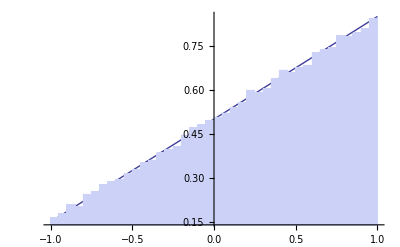

```mathematica
b=0.7;
Show[
Plot[2 Pi pLinaniso[u,b],{u,-1,1}],
Histogram[Map[(-1+√(1-2 b+b^2+4 b #))/b&,Table[RandomReal[],{i,1,100000}]],50,"PDF"]
]
Clear[b];
```